```mathematica
dprod[n_]:=Times@@IntegerDigits[n]
```

```mathematica
Tally[dprod/@Range[1000]]
```

{{1,3},{2,6},{3,6},{4,10},{5,6},{6,14},{7,6},{8,15},{9,10},{0,181},{10,8},{12,19},{14,8},{16,15},{18,19},{15,8},{21,8},{24,25},{27,9},{20,11},{28,11},{32,14},{36,24},{25,4},{30,14},{35,8},{40,14},{45,11},{42,14},{48,23},{54,17},{49,4},{56,14},{63,11},{64,11},{72,26},{81,7},{50,3},{60,12},{70,6},{80,9},{90,12},{84,12},{96,15},{108,15},{98,3},{112,9},{126,12},{128,6},{144,18},{162,9},{75,3},{105,6},{120,12},{135,6},{147,3},{168,12},{189,6},{192,9},{216,13},{243,3},{100,3},{140,6},{160,6},{180,9},{196,3},{224,6},{252,9},{256,3},{288,9},{324,6},{125,1},{150,3},{175,3},{200,3},{225,3},{210,6},{240,6},{270,6},{245,3},{280,6},{315,6},{320,3},{360,6},{405,3},{294,3},{336,6},{378,6},{384,3},{432,6},{486,3},{343,1},{392,3},{441,3},{448,3},{504,6},{567,3},{512,1},{576,3},{648,3},{729,1}}

```mathematica
Select[Union[Nest[dprod,#,4]&/@Range[1000000]],#<41&]
```

{0,1,2,3,4,5,6,7,8,9,12,15,16,18,20,32}

```mathematica
?Nest
```

Nest[f,expr,n] gives an expression with f applied n times to expr.

```mathematica
{0,1,2,3,4,5,6,7,8,9,12,15,16,20,32}
```

```mathematica
BaseForm[2^Range[100],3]
```

{2_3,11_3,22_3,121_3,1012_3,2101_3,11202_3,100111_3,200222_3,1101221_3,2210212_3,12121201_3,102020102_3,211110211_3,1122221122_3,10022220021_3,20122210112_3,111022121001_3,222122012002_3,1222021101011_3,10221112202022_3,21220002111121_3,120210012000012_3,1011120101000101_3,2100010202000202_3,11200021111001111_3,100100112222002222_3,200201002221012221_3,1101102012212102212_3,2202211102201212201_3,12112122212110202102_3,102002022201221111211_3,211011122110220000122_3,1122100021221210001021_3,10021200120220120002112_3,20120101011211010012001_3,111010202100122020101002_3,222021111201021110202011_3,1221120000102112221111022_3,10220010000212002212222121_3,21210020001201012202222012_3,120120110010102102112221101_3,1011010220020211212002212202_3,2022021210111200201012202111_3,11121120121000101102102111222_3,100020011012000202211212000221_3,200110022101001112200201001212_3,1100220121202010002101102010201_3,2201211020111020011202211021102_3,12110122110222110100112122112211_3,101221021221221220201002022002122_3,210212120220220211102011121012021_3,1121202011211211122211100012101112_3,10020111100200200022122200101210001_3,20110222201101100122022100210120002_3,110221222102202201021121201121010011_3,221220221212112102120020110012020022_3,1220211220202001212010110220101110121_3,10211200211111010201020221210202221012_3,21200101122222021102111220121112212101_3,120100210022221112212000211020002201202_3,1010201120122220002201001122110012110111_3,2021110011022210012102010021220101220222_3,11112220022122120101211020120210210211221_3,100002210122022010210122111011121121200212_3,200012121021121021121021222100020020101201_3,1100102012120012120012120221200110110210102_3,2200211102010102010102011220100220221120211_3,12101122211020211020211100210201211220011122_3,101210022122111122111122201121110200210100021_3,210120122022000022000022110012221101120200112_3,1121011021121000121000121220102212210011101001_3,10012022120012001012001020210212202120022202002_3,20101122010101002101002111121202112010122111011_3,110210021020202011202012000020112001021021222022_3,221120112111111100111101000111001002112120221121_3,1220011001222222200222202000222002012002011220012_3,10210022010222222101222111001221011101011100210101_3,21120121021222221210221222010212022202022201120202_3,120011012120222220121220221021201122111122110011111_3,1010022102011222211020211212120110022000021220022222_3,2020121211100222122111200202010220121000120210122221_3,11111020122201222022000101111021211012001011121022212_3,22222111022110221121000202222120122101002100012122201_3,122221222121221220012001112222011021202011200102022102_3,1022220222020220210101010002221022120111100100211121211_3,2122211221111211120202020012212122010222200201200020122_3,12022200220000200011111110102202021021222101110100111021_3,101122101210001100022222220212111112120221202220200222112_3,210021210120002200122222211202000002011220112211101222001_3,1120120121010012101022222200111000011100211002122210221002_3,10011011012020101202122222100222000022201122012022121212011_3,20022022101110210112022221201221000122110021101122020201022_3,110121121202221121001122220110212001021220112210021111102121_3,221020020112220012010022210221201002120211002120112222212012_3,1212110111002210101020122121220102012011122012011002222201101_3,10201220222012120202111022020210211101100021101022012222102202_3,21110211221102011111222121111121122202200112202121102221212111_3,112221200212211100000222020000020022112101002112012212220201222_3,1002220101202122200001221110000110122001202012001102202211110221_3}

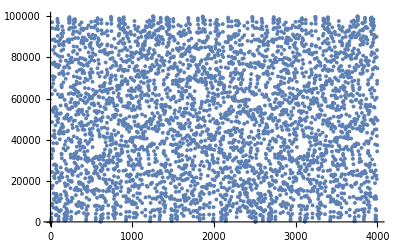

```mathematica
ListPlot@(Mod[2^Range[4000],100000])
Tally[dprod/@(Mod[2^Range[400000],1000000])]
```